# PROJEKTNA NALOGA PRI PREDMETU ROM: Dolžina sončne svetlobe na dan skozi leto

V seminarski nalogi pri predmetu Računalniška orodja v matematiki bom predstavila kako je dolžina sončne svetlobe na dan skozi celo leto sinusna/kosinusna krivulja.

Zato bomo najprej ponovili sinusno in kosinusno funkcijo.

## SINUSNA IN KOSINUSNA FUNKCIJA

Najprej si oglejmo formulo sinusne funkcije:

```mathematica
f[a_,b_,c_,d_,x_]:=a*Sin[b*x+c]+d
```

Sedaj si oglejmo kaj vse nastopa v zgornji funkciji:
a ... amplituda sinusa (t.j. za koliko sinus raztegnemo po y-osi)
b ... frekvenca sinusa (t.j. za koliko sinus raztegnemo po x-osi)
c ... premik sinusa po x-osi
d ... premik sinusa po y-osi

Poglejmo kako to izgleda pri risanju grafa:

```mathematica
Manipulate[Plot[f[a,b,c,d,x],{x,0,5*Pi}],{{a,1,"Amplituda"},-3,3},{{b,1,"Frekvenca"},0.1,2,0.1},{{c,0,"Premik po x-osi"},-3,3},{{d,0,"Premik po y-osi"},-3,3},Paneled->False]
```

Sedaj si še poglejmo kosinusno funkcijo:

```mathematica
h[a_,b_,c_,d_,x_]:=a*Cos[b*x+c]+d
```

Oglejmo kaj vse nastopa v zgornji funkciji:
a ... amplituda kosinusa (t.j. za koliko kosinus raztegnemo po y-osi)
b ... frekvenca kosinusa (t.j. za koliko kosinus raztegnemo po x-osi)
c ... premik kosinusa po x-osi
d ... premik kosinusa po y-osi

Poglejmo kako to izgleda pri risanju grafa:

```mathematica
Manipulate[Plot[h[a,b,c,d,x],{x,0,5*Pi}],{{a,1,"Amplituda"},-3,3},{{b,1,"Frekvenca"},0.1,2,0.1},{{c,0,"Premik po x-osi"},-3,3},{{d,0,"Premik po y-osi"},-3,3},Paneled->False]
```

Kot lahko opazimo je grav premaknjenega kosinusa enak sinusnemu grafu. Torej lahko sinus zapišemmo kot premaknjeni kosinus ali pa kosinus zapišemo kot premaknjeni sinus.

Poglejmo kako lahko to preverimo z enačbami in s pomočjo krožnice:

```mathematica
Manipulate[ContourPlot[{1==x^2+y^2,x==a,y==Sqrt[1-a^2]},{x,-1,1},{y,-1,1},Axes->True,Frame->False],{{a,0.5,"Spreminjanje koordinate x"},0,1},Paneled->False]
```

Če definiramo x in y:

```mathematica
X[t_]:=Cos[t]
Y[t_]:=Sin[t]
```

Potem vidimo, da veljajo naslednje enačbe:

```mathematica
TrigExpand[Sin[Pi/2-u]]
```

Cos[u]

```mathematica
TrigExpand[Cos[Pi/2-u]]
```

Sin[u]

```mathematica
TrigExpand[Sin[Pi-u]]
```

Sin[u]

```mathematica
TrigExpand[Cos[Pi-u]]
```

-Cos[u]

Vidimo torej, da lahko sinus izrazimo s kosinusom in obratno.
Sicer nam pomagajo naslednje enačbe:
(sinx)^2+(cosx)^2=1

```mathematica
TrigExpand[Sin[2*u]]
```

2 Cos[u] Sin[u]

```mathematica
TrigExpand[Cos[2*u]]
```

Cos[u]^2-Sin[u]^2

Sedaj, ko smo ponovili osnove sinusne in kosinusne funnkcije pa se osredotočimo na snov, ki je tema te seminarske naloge.

## Dolžina sončne svetlobe v dnevu skozi celo leto

Za ta del seminarske se bom naslonila na članka, ki sem ju najdla na internetu:
-https://static1.squarespace.com/static/59471704440243a2a0adc0e0/t/5c99157761179e00016c416d/1553536375355/daylight+hours+and+trigonometry.pdf
-https://www.sccollege.edu/Departments/MATH/Documents/Math%20170/06-06-36_Phase_Shift;_Sinusoidal_Curve_Fitting.pdf
Število dni na leto si bomo za letošnje leto (2019) izbrali 365 dni.

```mathematica
dniNaLeto=365
```

365

Iz spletne strani https://www.timeanddate.com/sun/slovenia/ljubljana?month=12&year=2019 sem dobila podatek za prvi zimski dan, ki pri naši funkciji predstavlja minimum.
Prvi zimski dan je bil na 22.12.2019.

```mathematica
prviZimskiDan=356
```

356

Iz spletne strani prepišemo uro sončnega vzhoda.

```mathematica
zacDec=7.683
```

7.683

Iz spletne strani prepišemo uro sončnega zahoda.

```mathematica
konDec=16.317
```

16.317

```mathematica
min=konDec-zacDec
```

8.634

Iz spletne strani https://www.timeanddate.com/sun/slovenia/ljubljana?month=6&year=2019 sem dobila podatek za prvi poletni dan, ki pri naši funkciji predstavlja maksimum.
Prvi poletni dan je bil na 21.06.2019.

```mathematica
prviPoletniDan=172
```

172

Iz spletne strani prepišemo uro sončnega vzhoda.

```mathematica
zacJun=5.167
```

5.167

Iz spletne strani prepišemo uro sončnega zahoda.

```mathematica
konJun=20.933
```

20.933

```mathematica
maks=konJun-zacJun
```

15.766

Pri podatkih nisem upoštevala premika ure, ker nas zanima samo maksimalno in minimalno število ur dnevne svetlobe. Na ta dva podatka pa ura začetka in konca dnevne svetlobe ne vpliva.
Sedanj imamo že skoraj vse podatke za zapis naše sinusne in kosinusne funkcije. Sedaj bomo še izračunali a, b, c in d.

Začeli bomo s premikom dol/gor, ker ga je najlažje izračunati.

```mathematica
d=(maks+min)/2
```

12.2

Sedaj lahko izračunamo a, ki je razlika med maksimalno vrednostjo in d.

```mathematica
a=maks-d
```

3.566

Nadaljevali bomo z izračunom periode.

```mathematica
perioda=(2*Pi)/365
```

(2 π)/365

Najprej bomo zapisali kosinusno funkcijo, saj se začne pri maksimumu in je potemtakem hitreje zapisati predpis za tako funkcijo.

```mathematica
c1=prviPoletniDan*perioda
```

(344 π)/365

```mathematica
k[u_]:=h[a,perioda,-c1,d,u]
```

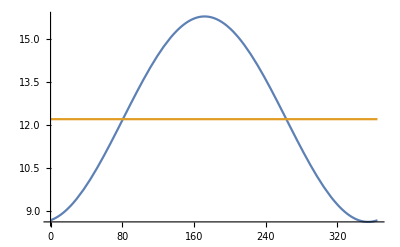

```mathematica
Plot[{k[x],y=d},{x,0,365}]
```

Sedaj pa lahko to še zapišemo s sinusno funkcijo. Zgornje podatke zrdužimo z znanjem, da je cos(Pi - x) = sin(x). Torej mormamo podatke prilagoditi in zato izračunajmo c, ki se edini spremeni.

```mathematica
c2=Solve[f[a,perioda,-1*c*perioda,d,350]==min,c][[1,1,2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

76.25

```mathematica
s[u_]:=f[a,perioda,-c2*perioda,d,u]
```

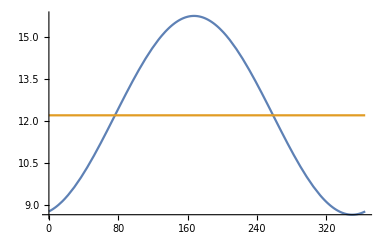

```mathematica
Plot[{s[x],y=d},{x,0,365}]
```

Opazimo, da grafa čisto malo odstopata drug od drugega in, če računamo s sinusno funkcijo pride do odstopanja. To lahko pripišemo zaokroževanju in numeričnemu računanju.

Sedaj izračunajmo še enakonočje in preverimo, da sta 1. poletni dan ter 1. zimski dan maksimum in minimum.

```mathematica
Solve[k[x]==12.2,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-101.75},{x→80.75}}

Prvo enakonočje je na 80-ti dan v letu, kar pride na 21.03. in drugo enakonočje je na 365-101=264-ti dan, kar je 21.09.

```mathematica
D[k[x],x]/.x->172
```

0.

```mathematica
D[k[x],x]/.x->356
```

0.00158489

Pri minimumu opazimo, da ne dobimo točno ničle. To se lahko zgodi zaradi predhodnega zaokroževanja.

Ta naša funkcija je uporabna samo za naše mesto (Ljubljana), saj se dolžina sončnih ur spreminja glede na geografsko širino in dolžino.
Opazimo tudi, da se samo amplituda spremija. Ko gremo proti ekvatorju se amplituda manjša in bolj kot gremo proti polu se veča. Amplituda spremeni predznak, ko zamenjamo polobli in v ekvatorju je ta krivulja konstantna y = d.

```mathematica
Manipulate[Plot[{h[u,perioda,-c1,d,x],y=d},{x,0,365}, PlotRange->{0,25}],{{u,a, "Razlika med najkrajšim in najdaljšim dnem"},-12,12},Paneled->False]
```